# PRACTICAL 1 : BISECTION METHOD

## Ques 1 : Perform 14 iterations to find a root of x^3-17=0

i | ai | bi | ci | f[ci]
0 | 2 | 3 | 2.5 | -1.375
1 | 2.5 | 3 | 2.75 | 3.79688
2 | 2.5 | 2.75 | 2.625 | 1.08789
3 | 2.5 | 2.625 | 2.5625 | -0.173584
4 | 2.5625 | 2.625 | 2.59375 | 0.449554
5 | 2.5625 | 2.59375 | 2.57813 | 0.136097
6 | 2.5625 | 2.57813 | 2.57031 | -0.0192142
7 | 2.57031 | 2.57813 | 2.57422 | 0.0583236
8 | 2.57031 | 2.57422 | 2.57227 | 0.0195253
9 | 2.57031 | 2.57227 | 2.57129 | 0.0001482
10 | 2.57031 | 2.57129 | 2.5708 | -0.00953482
11 | 2.5708 | 2.57129 | 2.57104 | -0.00469377
12 | 2.57104 | 2.57129 | 2.57117 | -0.0022729
13 | 2.57117 | 2.57129 | 2.57123 | -0.00106238
14 | 2.57123 | 2.57129 | 2.57126 | -0.000457096

Root after 15 iterations is 2.57126

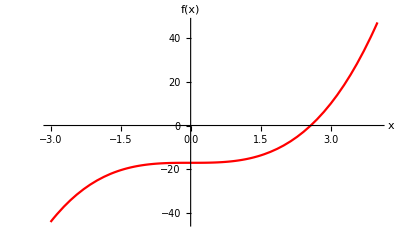

```mathematica
f[x_]:=x^3-17
a=2;
b=3;
c=N[(a+b)/2];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in teh given interal"],
OutputDetails={{i,a,b,c,f[c]}};
While[i<14,
If[f[a]*f[c]<0, b=c, a=c];
c=N[(a+b)/2];
i++;
OutputDetails=Append[OutputDetails, {i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails, 
TableHeadings->{None, {"i", "ai", "bi", "ci", "f[ci]"}}], 6]];
Print["Root after ", 15, " iterations is ", NumberForm[c,6]];
Plot[f[x], {x, -3,4}, PlotStyle->{Red}, AxesLabel-> {"x", "f(x)"}]
]
```

## Ques 2 : Perform 15 iterations to find a root of Cos(x)=x.

i | ai | bi | ci | f[ci]
0 | 0 | 1 | 0.5 | 0.377583
1 | 0.5 | 1 | 0.75 | -0.0183111
2 | 0.5 | 0.75 | 0.625 | 0.185963
3 | 0.625 | 0.75 | 0.6875 | 0.0853349
4 | 0.6875 | 0.75 | 0.71875 | 0.0338794
5 | 0.71875 | 0.75 | 0.734375 | 0.00787473
6 | 0.734375 | 0.75 | 0.742188 | -0.00519571
7 | 0.734375 | 0.742188 | 0.738281 | 0.00134515
8 | 0.738281 | 0.742188 | 0.740234 | -0.00192387
9 | 0.738281 | 0.740234 | 0.739258 | -0.000289009
10 | 0.738281 | 0.739258 | 0.73877 | 0.000528158
11 | 0.73877 | 0.739258 | 0.739014 | 0.000119597
12 | 0.739014 | 0.739258 | 0.739136 | -0.0000847007
13 | 0.739014 | 0.739136 | 0.739075 | 0.0000174493
14 | 0.739075 | 0.739136 | 0.739105 | -0.0000336253

Root after 15 iterations is 0.739105

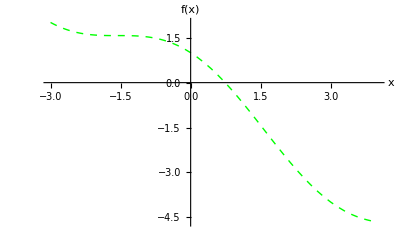

```mathematica
f[x_]:=Cos[x]-x
a=0; b=1; c=N[(a+b)/2];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in teh given interal"],
OutputDetails={{i,a,b,c,f[c]}};
While[i<14,
If[f[a]*f[c]<0, b=c, a=c];
c=N[(a+b)/2];
i++;
OutputDetails=Append[OutputDetails, {i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails, 
TableHeadings->{None, {"i", "ai", "bi", "ci", "f[ci]"}}], 6]];
Print["Root after ", 15, " iterations is ", NumberForm[c,6]];
Plot[f[x], {x, -3,4}, PlotStyle->{Green, Dashed , Thick}, AxesLabel-> {"x", "f(x)"}]
]
```